```mathematica
data=Import["/Users/tomasdecaminobeck/Downloads/calibrationAccelerometer.txt","CSV"];
```

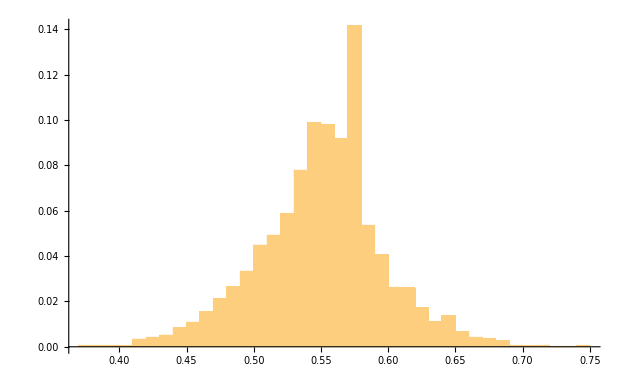

```mathematica
Histogram[data[[All,1]],300,"Probability"]
```

```mathematica
Sort[Tally[data[[All,1]]]]
```

{{0.37,4},{0.38,4},{0.39,4},{0.4,3},{0.41,21},{0.42,26},{0.43,32},{0.44,52},{0.45,67},{0.46,95},{0.47,131},{0.48,163},{0.49,206},{0.5,277},{0.51,304},{0.52,363},{0.53,481},{0.54,610},{0.55,604},{0.56,567},{0.57,874},{0.58,331},{0.59,250},{0.6,162},{0.61,160},{0.62,106},{0.63,69},{0.64,84},{0.65,41},{0.66,26},{0.67,22},{0.68,16},{0.69,4},{0.7,3},{0.71,4},{0.72,1},{0.73,1},{0.74,4}}

```mathematica
Mean[data[[All,1]]]
```

0.545987

```mathematica
dataDistance=Import["/Users/tomasdecaminobeck/Downloads/Caminada1.txt","CSV"];
```

```mathematica
Dimensions[dataDistance]
```

{75,4}

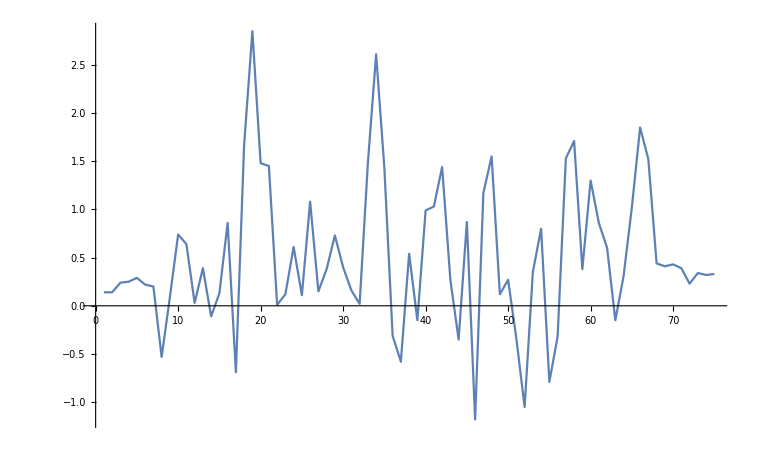

```mathematica
ListLinePlot[dataDistance[[All,1]], InterpolationOrder->1,PlotRange->All]
```

```mathematica
Manipulate[Show[ListLinePlot[dataDistance[[All,1]], InterpolationOrder->n,PlotRange->All],ListPlot[dataDistance[[All,1]]],PlotLabel->Floor[n]],{n,1,50}]
```

```mathematica
f=Interpolation[dataDistance[[All,1]],InterpolationOrder->3]
```

InterpolatingFunction[{{1., 75.}}, <>]

```mathematica
Integrate[f[x],{x,1,74}]
```

37.3483